```mathematica
ClearAll["Global`*"]
NotebookDirectory[] ;
SetDirectory[%];
```

```mathematica
udata=ReadList["Geff.dat", {Number,Number}];
```

```mathematica
u=Interpolation[udata];
ru[r_]:=Piecewise[{{1,0≤r<0.01},{u[r],0.01<=r≤109.99},{1,r>109.99}}]
```

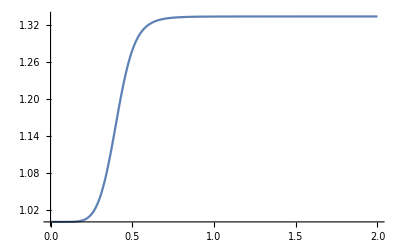

```mathematica
Plot[ru[r],{r,0,2}]
```

```mathematica
(*du=D[u[r],r];
rdu[r_]:=Piecewise[{{0,0≤r<0.01},{du,0.01<=r≤109.99},{0,r>109.99}}]*)
```

```mathematica
(*LogLinearPlot[rdu[r],{r,0,140},PlotRange->All]*)
```

```mathematica
(*rdudata=Table[{x,rdu[x]},{x,0,1,0.01}];
rduf=Interpolation[rdudata];
rrduf[r_]:=Piecewise[{{rduf[r],0<=r≤1},{0,r>1}}]*)
```

```mathematica
(*LogLinearPlot[rrduf[r],{r,0,140},PlotRange->All]*)
```

```mathematica
(*a1[b_]:=b*NIntegrate[((1+ru[r])*ru[r])/r^3/.r->√(b^2+z^2),{z,0,∞}]*)
(*LogLinearPlot[a1[b],{b,0.0001,100},PlotRange->All]*)
```

```mathematica
(*a2[b_]:=b*NIntegrate[((1+ru[r])*rrduf[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}]*)
(*LogLinearPlot[a2[b],{b,0.0001,100},PlotRange->All]
*)
```

```mathematica
(*a3[b_]:=b*NIntegrate[(ru[r]*rrduf[r])/r^2/.r->√(b^2+z^2),{z,0,Infinity}]*)
(*LogLinearPlot[a3[b],{b,0.0001,100},PlotRange->All]*)
```

```mathematica
(*Ibdata=Table[{b,a1[b]-a2[b]-a3[b]},{b,0.01,110,0.01}];*)
```

```mathematica
(*Export["Ibdata.txt",Ibdata,"Table"];*)
```

```mathematica
Ibdata=ReadList["Ibdata.txt",{Number,Number}];
```

```mathematica
rIb=Interpolation[Ibdata];
```

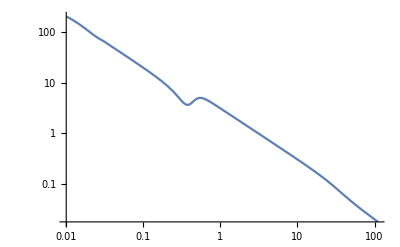

```mathematica
rrIb[b_]:=Piecewise[{{2/b,b<-110},{-rIb[-b],-110≤b≤-0.01},{2/b,-0.01<b<0.01},{rIb[b],0.01<=b≤110},{2/b,b>110}}];
LogLogPlot[rrIb[b],{b,0.01,110},PlotRange->All]
```

```mathematica
(*LogLogPlot[{a1[b]-a2[b]-a3[b],rrIb[b]},{b,0.01,110},PlotRange->All]*)
```

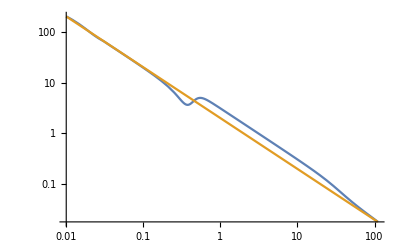

```mathematica
LogLogPlot[{rrIb[b],2/b},{b,0.01,110},PlotRange->All]
```

```mathematica
zl=1;
zs=2;
om=0.3;
h0=70;(*km s^-1 Mpc^-1*)
h0c=68;(*km s^-1 Mpc^-1*)
c=3*10^5;(*km s^-1*)
(*Mpc=30.85678*10^18 km*)
(*Msun=1.9891*10^30 kg*)
(*G=6.673*10^-11 m^3 kg^-1 s^-2*)
G=6.673*10^-20*1.9891*10^30;(*km^3 Msun^-1 s^-2*)
M=10^12;(*Msun*)
```

```mathematica
H[t_]:=Sqrt[1-om+om *(1+t)^3];
DA[z_]:=c/h0 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DAc[z_]:=c/h0c 1/(1+z)NIntegrate[1/H[t],{t,0,z}];
DA2[z1_,z2_]:=c/h0 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];
DA2c[z1_,z2_]:=c/h0c 1/(1+z2)NIntegrate[1/H[t],{t,z1,z2}];

DA[zl]
DA[zs]
DA2[zl,zs]

DAc[zl]
DAc[zs]
DA2c[zl,zs]
```

1653.06

1727.82

625.777

1701.68

1778.63

644.183

```mathematica
thetaE=√((4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs]))
thetaEc=√((4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs]))
```

6.47201×10^-6

6.37889×10^-6

```mathematica
phihGR[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])NIntegrate[-1/(√((DA[zl]*x)^2+z^2)),{z,0,Infinity}];
phihGRc[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zl]*DAc[zs])NIntegrate[-1/(√((DAc[zl]*x)^2+z^2)),{z,0,Infinity}];
phihMG[x_]:=(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zl]*DA[zs])NIntegrate[(-(1+ru[r])*ru[r])/(2*r)/.r->√((DA[zl]*x)^2+z^2),{z,0,Infinity}];
```

```mathematica
n=2000;
```

```mathematica
TDGR=Table[0,{n}];
TDGRc=Table[0,{n}];
TDMG=Table[0,{n}];
```

```mathematica
For[i=1,i≤n,i++,y=0.1+0.001*i;thetaGR=theta/.NSolve[theta-y*thetaE==(4G*M)/c^2*1/(30.85678*10^18)*DA2[zl,zs]/(DA[zs]DA[zl])*1/theta,theta];thetaGRc=theta/.NSolve[theta-y*thetaEc==(4G*M)/c^2*1/(30.85678*10^18)*DA2c[zl,zs]/(DAc[zs]DAc[zl])*1/theta,theta];
thetaGRp=thetaGR[[1]];
thetaGRm=thetaGR[[2]];
alphaGRp=thetaGRp-y*thetaE;
alphaGRm=thetaGRm-y*thetaE;
DettGR=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2(alphaGRp)^2-1/2(alphaGRm)^2-(phihGR[thetaGRp]-phihGR[thetaGRm]));
TDGR[[i]]={y,Abs[DettGR]};
thetaGRpc=thetaGRc[[1]];
thetaGRmc=thetaGRc[[2]];
alphaGRpc=thetaGRpc-y*thetaEc;
alphaGRmc=thetaGRmc-y*thetaEc;
DettGRc=(1+zl)/c*30.85678*10^18*(DAc[zl]*DAc[zs])/DA2c[zl,zs](1/2(alphaGRpc)^2-1/2(alphaGRmc)^2-(phihGRc[thetaGRpc]-phihGRc[thetaGRmc]));
TDGRc[[i]]={y,Abs[DettGRc]};
thetaMGp=theta/.FindRoot[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(2G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),{theta,thetaGRp}];
thetaMGm=theta/.FindRoot[theta-y*thetaE==DA2[zl,zs]/DA[zs]*(2G*M)/c^2*1/(30.85678*10^18)*rrIb[b]/.b->(DA[zl]*theta),{theta,thetaGRm}];
alphaMGp=thetaMGp-y*thetaE;
alphaMGm=thetaMGm-y*thetaE;
DettMG=(1+zl)/c*30.85678*10^18*(DA[zl]*DA[zs])/DA2[zl,zs](1/2 alphaMGp^2-1/2 alphaMGm^2-(phihMG[thetaMGp]-phihMG[thetaMGm]));
TDMG[[i]]={y,Abs[DettMG]};]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {6.13224×10^28}. NIntegrate obtained -23562.6 and 19651.8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {6.13224×10^28}. NIntegrate obtained -23562.7 and 19651.9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {6.13224×10^28}. NIntegrate obtained -23562.6 and 19651.8 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

General::stop: Further output of StyleBox[RowBox[{\"NIntegrate\", \"::\", \"ncvb\"}], \"MessageName\"] will be suppressed during this calculation.

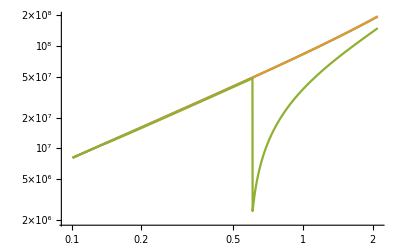

```mathematica
ListLogLogPlot[{TDGR,TDGRc,TDMG},Joined->True]
```

```mathematica
diffhc=Table[{TDGR[[i,1]],TDGR[[i,2]]-TDGRc[[i,2]]},{i,1,n}];
diffMG=Table[{TDGR[[i,1]],TDGR[[i,2]]-TDMG[[i,2]]},{i,1,n}];
```

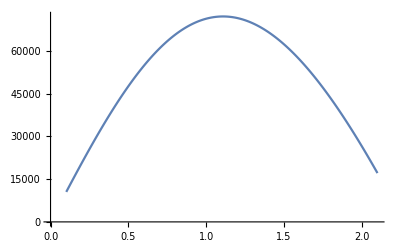

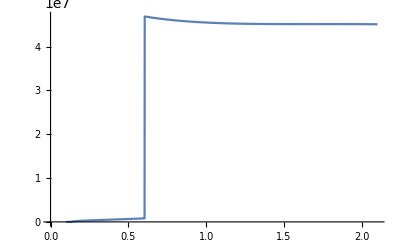

```mathematica
ListLinePlot[diffhc]
ListLinePlot[diffMG]
```

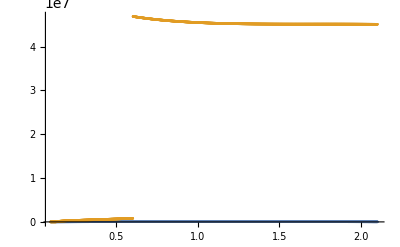

```mathematica
ListPlot[{diffhc,diffMG},PlotRange->All]
```